## 1D CellPlot:

### Initial Conditions:

```mathematica
basis={{1,0},{0.5,Sqrt[3]/2}}; (* A basis generating the lattice points. Length equal to dimension of lattice.*)
initialConditions1D={0,0,0,0,0,0,0,1,0,0,0,1,0,0,0}; (* Initial conditions. *)
rowLength[n_Integer]:=If[EvenQ[n],{n/2,n/2},{(n+1)/2,(n-1)/2}]; (*Specifies how many "odd" and "even" triangles are in our graphic. First value is odd trangles. *)
```

Triangular Cells 1D Case:

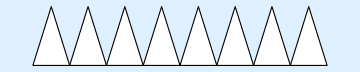

```mathematica
oddTriangles[basis_,initialConditions_]:=Module[{b1=basis[[1]],b2=basis[[2]],r=rowLength[Length[initialConditions]][[1]]-1},
Table[
{FaceForm[GrayLevel[1-initialConditions[[2*i+1]]]],EdgeForm[Black],Triangle[{i*b1,(i+1)*b1,i*b1+b2}]},
{i,0,r}]
]; (* Generates the "odd" traingles that can then be interpreted as Graphics objects. *)
Graphics[oddTriangles[basis,initialConditions1D],Background->LightBlue]
```

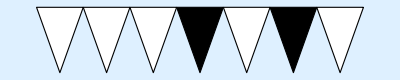

```mathematica
evenTriangles[basis_,initialConditions_]:=Module[{b1=basis[[1]],b2=basis[[2]],r=rowLength[Length[initialConditions]][[2]]-1},
Table[
{FaceForm[GrayLevel[1-initialConditions[[2*(i+1)]]]],EdgeForm[Black],
Triangle[{(i+1)*b1+b2,(i+1)*b1,i*b1+b2}]},
{i,0,r}]
];(* Generates the "even" traingles that can then be interpreted as Graphics objects. *)
Graphics[evenTriangles[basis,initialConditions1D],Background->LightBlue]
```

```mathematica
triangleCAList[basis_,initialConditions_]:=
Riffle[
oddTriangles[basis,initialConditions],evenTriangles[basis,initialConditions]
];  (* Combines the lists of "odd" and "even" triangles into a new list. *)
```

### 1D New Generation Rule:

```mathematica
ruleTable[rule_Integer,neighborCount_Integer:5]:=Reverse[PadLeft[IntegerDigits[rule,2],2^neighborCount]]; (* Given a number and Moore neighborhood size generates a rule table. *)
ruleTable[30,3]
```

{0,1,1,1,1,0,0,0}

```mathematica
nextStep[initialConditions_List,rule_Integer,neighborCount_Integer:5]:=Module[{a=neighborCount/2,b=Floor[neighborCount/2],l=Length[initialConditions]},
Table[
ruleTable[rule,neighborCount][[FromDigits[
If[i<a,PadLeft[Take[initialConditions,{1,i+b}],neighborCount],
If[i>l-a,PadRight[Take[initialConditions,{i-b,l}],neighborCount],Take[initialConditions,{i-b,i+b}]]],2]+1]]
,{i,1,l}]
]; (*Generates the state at time t+1 given state at time t. *)
```

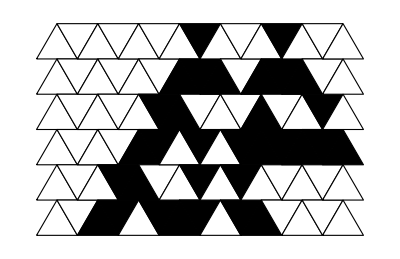

```mathematica
triangularCA[basis_,initialConditions_List,iterations_Integer,rule_Integer,neighborCount_Integer:5]:=Module[{d=basis[[1]][[2]]/2-basis[[2]][[2]],r=rowLength[Length[initialConditions]]},
Graphics[
Table[
Translate[triangleCAList[basis,Nest[nextStep[#,rule,neighborCount]&,initialConditions,i]],{0,d*i}],{i,0,iterations}
],
ImageSize->50*r[[1]]]
]; (* Plots a 1D triangular CA *)
triangularCA[{{1,0},{0.5,Sqrt[3]/2}},initialConditions1D,5,30,3]
```

## 2D CellPlot:

### 2D Initial Conditions:

```mathematica
initialConditions2D=SparseArray[{{1,1}->1,{2,5}->1,{3,10}->1},{3,11}];
```

```mathematica
latticePoints[basis_,dimensions_]:=Flatten[
Table[(i*basis[[1]]+j*basis[[2]]),{i,0,dimensions[[1]]-1},{j,0,dimensions[[2]]-1}]
,1];
latticePointsPlot[points_]:=ListPlot[points,Axes->False]; (* Generates a list of 2D lattice points given a basis. *)
```

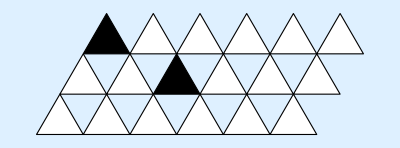

{FaceForm[GrayLevel[1]],EdgeForm[GrayLevel[0]],Triangle[{{0.,0},{1.,0},{0.5,(√3)/2}}]}

```mathematica
oddTriangleCells[basis_,state_]:=Module[{b1=basis[[1]],b2=basis[[2]],d1=Dimensions[state][[1]],
d2=If[EvenQ[Dimensions[state][[2]]],(Dimensions[state][[2]])/2,(Dimensions[state][[2]]+1)/2],flipped=Reverse[state,1]},
Table[
{FaceForm[GrayLevel[1-flipped[[j+1]][[2i+1]]]],EdgeForm[Black],Triangle[{i*b1+j*b2,(i+1)*b1+j*b2,i*b1+(j+1)*b2}]}
,{i,0,d2-1},{j,0,d1-1}]
]; (* Generates a list of "odd" triangular cells of a 2D CA, given a lattice basis and initial conditions. Note they are "flipped" for now. *)
Graphics[oddTriangleCells[basis,initialConditions2D],Background->LightBlue]
oddTriangleCells[basis,initialConditions2D][[1,1]]
```

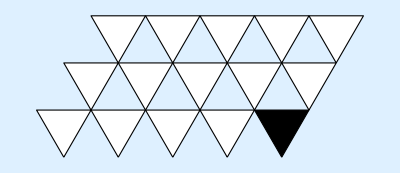

```mathematica
evenTriangleCells[basis_,state_]:=Module[{b1=basis[[1]],b2=basis[[2]],d1=Dimensions[state][[1]],
d2=If[EvenQ[Dimensions[state][[2]]],(Dimensions[state][[2]])/2,(Dimensions[state][[2]]-1)/2],flipped=Reverse[state,1]},
Table[
{FaceForm[GrayLevel[1-flipped[[j+1]][[2(i+1)]]]],EdgeForm[Black],Triangle[{(i+1)*b1+j*b2,i*b1+(j+1)*b2,(i+1)*b1+(j+1)*b2}]}
,{i,0,d2-1},{j,0,d1-1}]
]; (* Generates a list of "even" triangular cells of a 2D CA, given a lattice basis and initial conditions. Note they are "flipped" for now. *)
Graphics[evenTriangleCells[basis,initialConditions2D],Background->LightBlue]
```

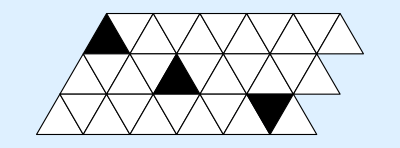

```mathematica
triangleCells[basis_,state_]:=Module[{flipped=Reverse[state,1]},
Riffle[
oddTriangleCells[basis,state],evenTriangleCells[basis,state]
]
]; (* Combines the lists of "odd' and "even" trianular cells to make a 2D triangular CA. They will now no longer be "flipped"*)
Graphics[triangleCells[{{1,0},{0.5,Sqrt[3]/2}},initialConditions2D],Background->LightBlue]
```

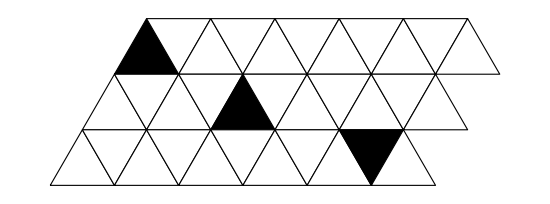
-Graphics-(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0)

{FaceForm[GrayLevel[1]],EdgeForm[GrayLevel[0]],Triangle[{{0.,0},{1.,0},{0.5,(√3)/2}}]}

```mathematica
triangleCellPlot[basis_,state_]:=
Graphics[triangleCells[basis,state],ImageSize->50*Dimensions[state][[2]]]; (*Displays the state of a 2D triangular CA at time t. *)
Row[{triangleCellPlot[basis,initialConditions2D],initialConditions2D//MatrixForm}]
triangleCells[basis,initialConditions2D][[1,1]]
```

### 2D New Generation Rule:

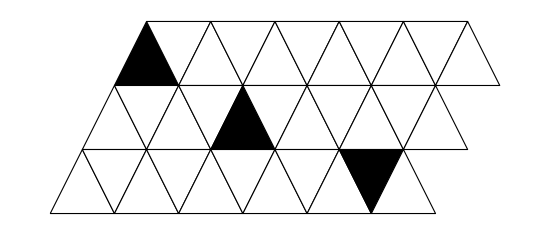

```mathematica
state=triangleCells[{{1,0},{0.5,1}},initialConditions2D];
triangleCellPlot[{{1,0},{0.5,1}},initialConditions2D]
```

```mathematica
vonNeumannNeighborhood[cell_]:=Module[{x=cell[[1]],y=cell[[2]]},
If[OddQ[cell[[1]]],
{{x-1,y},{x,y},{x+1,y},{x+1,y-1}},
{{x-1,y+1},{x-1,y},{x,y},{x+1,y}}]
];
cellState[cell_,state_]:=If[TrueQ[state[[cell[[1]],Dimensions[state][[2]]+1-cell[[2]],1]]== FaceForm[Black]],1,0];
cellState[{10,3},state]
```

1

```mathematica
neighborhoodState[cell_,state_]:=Do
```

```mathematica
a=neighborhoodState[{5,2},initialConditions2D]
```

cellState[#1,SparseArray[…]]/@vonNeumannNeighborhood[{5,2}]&

```mathematica
a[[11]]
```

{{FaceForm[GrayLevel[1]],EdgeForm[GrayLevel[0]],Triangle[{{5.,0},{6.,0},{5.5,(√3)/2}}]},{FaceForm[GrayLevel[1]],EdgeForm[GrayLevel[0]],Triangle[{{5.5,(√3)/2},{6.5,(√3)/2},{6.,√3}}]},{FaceForm[GrayLevel[1]],EdgeForm[GrayLevel[0]],Triangle[{{6.,√3},{7.,√3},{6.5,(3 √3)/2}}]}}

```mathematica
Neigh
```

```mathematica
f=FaceForm[Black]
```

FaceForm[GrayLevel[0]]

```mathematica
Binary
```

1